Probability tuples for the generation of NM-conforming states

```mathematica
NMcPT[𝒩_]:=Module[{list=RandomReal[{0,1},𝒩]},list/Total[list]];
```

Probability tuples for the generation of NM-violating states

```mathematica
NMvPT[𝒩_]:=Module[{list=RandomReal[{-1,1},𝒩-1]},last=1-Total[list];Flatten[{list,last}]];
```

#### N=2

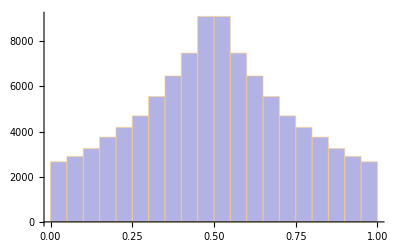

```mathematica
𝓃=1;𝒽ℓ={};While[𝓃≤50000,AppendTo[𝒽ℓ,NMcPT[2]];𝓃++];Histogram[Flatten[𝒽ℓ],ChartStyle->{Opacity[0.3,Darker[Blue]]}]
```

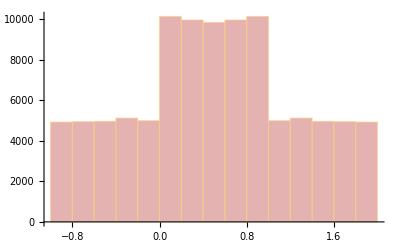

```mathematica
𝓃=1;𝒽ℓ={};While[𝓃≤50000,AppendTo[𝒽ℓ,NMvPT[2]];𝓃++];Histogram[Flatten[𝒽ℓ],ChartStyle->{Opacity[0.3,Darker[Red]]}]
```

#### N=3

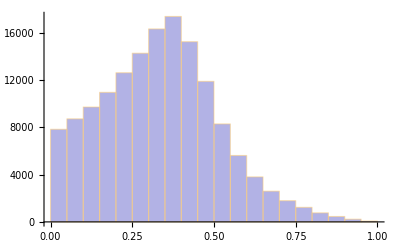

```mathematica
𝓃=1;𝒽ℓ={};While[𝓃≤50000,AppendTo[𝒽ℓ,NMcPT[3]];𝓃++];Histogram[Flatten[𝒽ℓ],ChartStyle->{Opacity[0.3,Darker[Blue]]}]
```

```mathematica
ListPointPlot3D[𝒽ℓ,BoxRatios->{1,1,1},PlotStyle->Darker[Blue],ImageSize->500]
```

-Graphics3D-

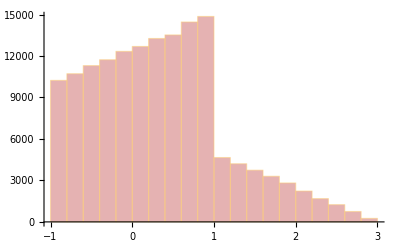

```mathematica
𝓃=1;𝒽ℓ={};While[𝓃≤50000,AppendTo[𝒽ℓ,NMvPT[3]];𝓃++];Histogram[Flatten[𝒽ℓ],ChartStyle->{Opacity[0.3,Darker[Red]]}]
```

```mathematica
ListPointPlot3D[𝒽ℓ,BoxRatios->{1,1,1},PlotStyle->Darker[Red],ImageSize->500]
```

-Graphics3D-

#### N=4

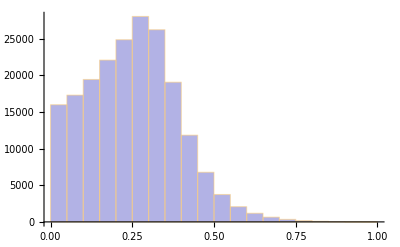

```mathematica
𝓃=1;𝒽ℓ={};While[𝓃≤50000,AppendTo[𝒽ℓ,NMcPT[4]];𝓃++];Histogram[Flatten[𝒽ℓ],ChartStyle->{Opacity[0.3,Darker[Blue]]}]
```

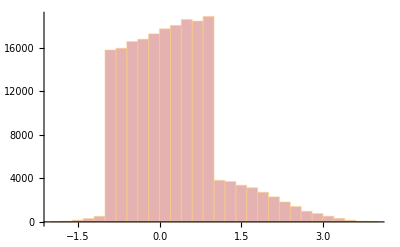

```mathematica
𝓃=1;𝒽ℓ={};While[𝓃≤50000,AppendTo[𝒽ℓ,NMvPT[4]];𝓃++];Histogram[Flatten[𝒽ℓ],ChartStyle->{Opacity[0.3,Darker[Red]]}]
```

#### N=5

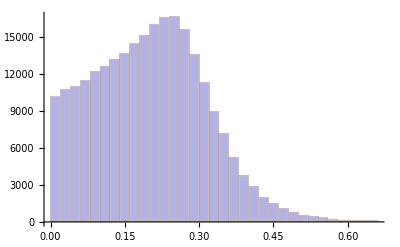

```mathematica
𝓃=1;𝒽ℓ={};While[𝓃≤50000,AppendTo[𝒽ℓ,NMcPT[5]];𝓃++];Histogram[Flatten[𝒽ℓ],ChartStyle->{Opacity[0.3,Darker[Blue]]}]
```

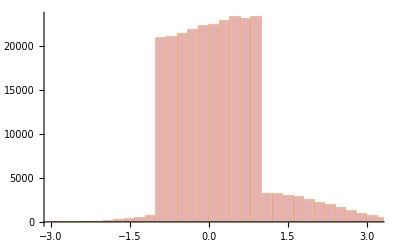

```mathematica
𝓃=1;𝒽ℓ={};While[𝓃≤50000,AppendTo[𝒽ℓ,NMvPT[5]];𝓃++];Histogram[Flatten[𝒽ℓ],ChartStyle->{Opacity[0.3,Darker[Red]]}]
```

#### N=10

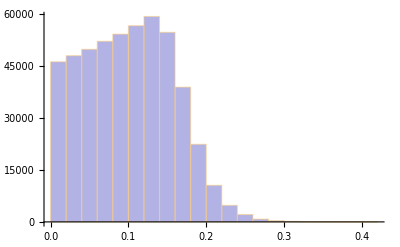

```mathematica
𝓃=1;𝒽ℓ={};While[𝓃≤50000,AppendTo[𝒽ℓ,NMcPT[10]];𝓃++];Histogram[Flatten[𝒽ℓ],ChartStyle->{Opacity[0.3,Darker[Blue]]}]
```

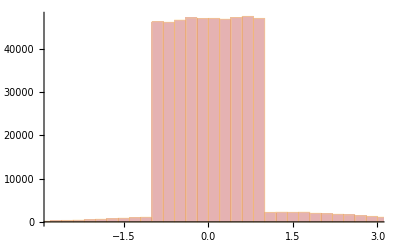

```mathematica
𝓃=1;𝒽ℓ={};While[𝓃≤50000,AppendTo[𝒽ℓ,NMvPT[10]];𝓃++];Histogram[Flatten[𝒽ℓ],ChartStyle->{Opacity[0.3,Darker[Red]]}]
```